```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Specifying some parameters*)
```

```mathematica
XL:=-20;
XR:=50
```

```mathematica
(*The objective here is to create a visual version of the touching plane sollution*)
```

```mathematica
(*h1[x_]:=Piecewise[{{1/2*1*x^2+(30-15)/10*x+15,x<=0},{15+(30-15)/10*x,0<x<10}},1/2*1*(x-10)^2+((30-15)/10)*(x-10)+30]*)(*Example 1, the Range for plotting Touching plane is {0,120}*)
```

```mathematica
h1[x_,a_,b_]:=x^4/4-a/3*x^3+(b+1/4)*a^2/2*x^2(*Example 2, the Range for plotting Touching plane is {0,100000}*)
```

```mathematica
Manipulate[Plot[h1[x,a,b],{x,XL,XR}],{a,0,100},{b,0,1/12}]
```

```mathematica
f[x_,a_,b_]=D[h1[x,a,b],x]
```

a^2 (1/4+b) x-a x^2+x^3

```mathematica
ans=0
```

0

```mathematica
Manipulate[soln = Solve[f[x,50,0.01]==s,x,Reals];check=x/.soln[[1]]; For[i=1,i<=Length[soln],i++,ans=x/.soln[[i]];If[h1[ans,50,0.01]-s*ans<=h1[check,50,0.01]-s*check,check=ans,ans=0]];Plot[{h1[y,50,0.01], s*(y-check)+h1[check,50,0.01]},{y,XL,XR},PlotRange->{0,60000}],{s,0,10000}]
```

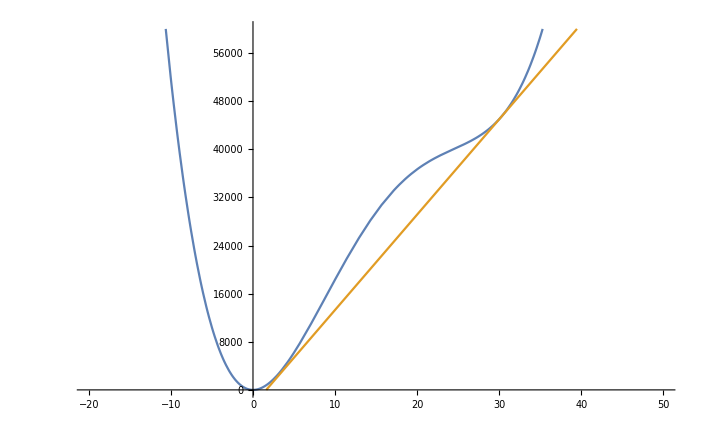

```mathematica
(*Vid=Animate[soln = Solve[f[x,50,0.01]==s,x,Reals];check=x/.soln[[1]]; For[i=1,i<=Length[soln],i++,ans=x/.soln[[i]];If[h1[ans,50,0.01]-s*ans<=h1[check,50,0.01]-s*check,check=ans,ans=0]];Plot[{h1[y,50,0.01], s*(y-check)+h1[check,50,0.01]},{y,XL,XR},PlotRange->{0,60000}],{s,0,10000}]
Export["Soft.mov",Vid]*)
soln = Solve[f[x,50,0.01]==1585,x,Reals];check=x/.soln[[1]]; For[i=1,i<=Length[soln],i++,ans=x/.soln[[i]];If[h1[ans,50,0.01]-1585*ans<=h1[check,50,0.01]-1585*check,check=ans,ans=0]];Plot[{h1[y,50,0.01], 1585*(y-check)+h1[check,50,0.01]},{y,XL,XR},PlotRange->{0,60000}]
```

```mathematica
(*Testing out the Minimization using for loop and if-else*)
```

```mathematica
s1=630
```

630

```mathematica
FindMinimum[h1[x,50,0.01]-s1*x,{x,30}]
```

{-322.179,{x→1.05268}}

```mathematica
soln = Solve[{x^3-50*x^2+(0.01+1/4)*50^2*x}==s1,x,Reals]
```

{{x→1.05268},{x→23.7767},{x→25.1707}}

```mathematica
check=x/.soln[[1]]
```

1.05268

```mathematica
h1[check,50,0.01]-s1*check
```

-322.179

```mathematica
ans=0
```

0

```mathematica
For[i=1,i<=Length[soln],i++,ans=x/.soln[[i]];If[h1[ans,50,0.01]-s1*ans<=h1[check,50,0.01]-s1*check,check=ans,Print[ans];ans=0]]
```

23.7767

25.1707

```mathematica
check
```

1.05268